```mathematica
ClearAll["Global`*"]
```

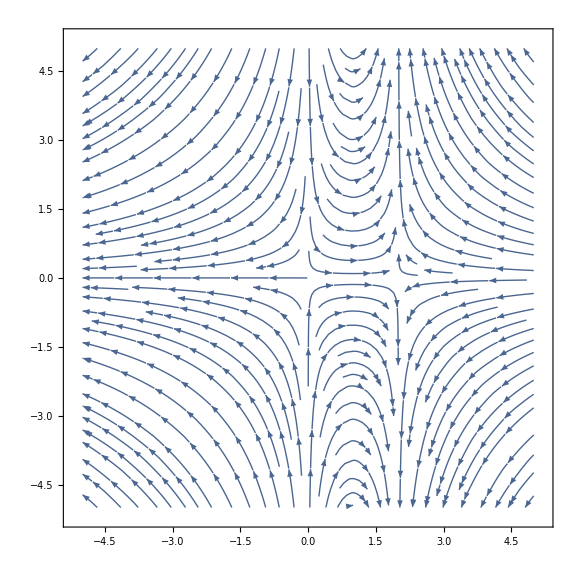

```mathematica
vecf=StreamPlot[{2x-x*x,-y+x*y},{x,-5,5},{y,-5,5},ImageSize->Large,AspectRatio->Automatic,StreamPoints->Fine]
```

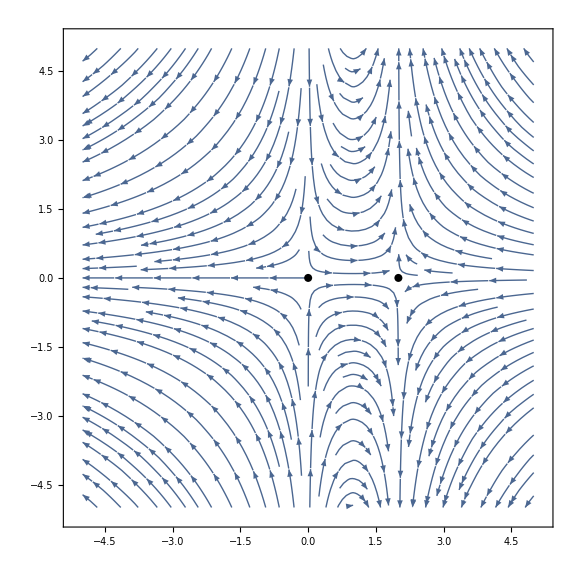

```mathematica
vecfComb=Show[vecf,Graphics[{PointSize[0.01],Point[{2,0}]}],Graphics[{PointSize[0.01],Point[{0,0}]}]]
```

```mathematica
Export["vecfComb.pdf",vecfComb]
```

vecfComb.pdf

```mathematica
DSolve[{x'[t]==2x[t]-x[t]^2,y'[t]==-y[t]+x[t]y[t]},{x[t],y[t]},t]
```

{{x[t]→(2 ⅇ^(2 t))/(ⅇ^(2 t)+ⅇ^(2 C[1])),y[t]→ⅇ^-t (ⅇ^(2 t)+ⅇ^(2 C[1])) C[2]}}

```mathematica
DSolve[y'[x]==(-y[x]+x*y[x])/(2x-x^2),y[x],x]
```

{{y[x]→C[1]/(√(2-x) √x)}}

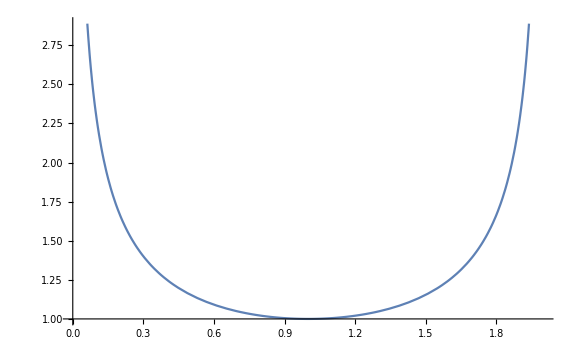

```mathematica
Plot[c/Sqrt[(2-x)x]/.c->1,{x,0,2},ImageSize->Large]
```

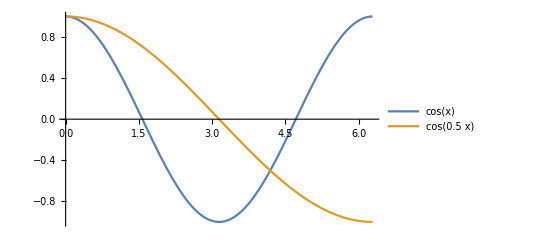

```mathematica
Plot[{Cos[x],Cos[0.5x]},{x,0,2Pi},PlotLegends->"Expressions"]
```

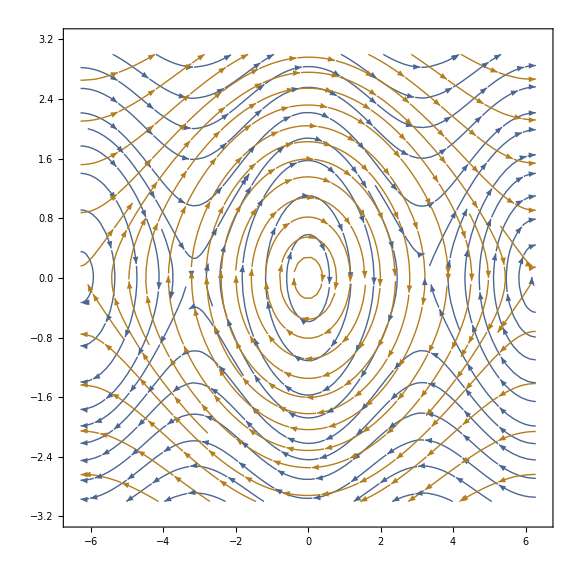

```mathematica
StreamPlot[{{y, -Sin[x]},{y, -Sin[0.5x]}},{x,-2Pi,2Pi},{y,-3,3},ImageSize->Large,Axes->True]
```

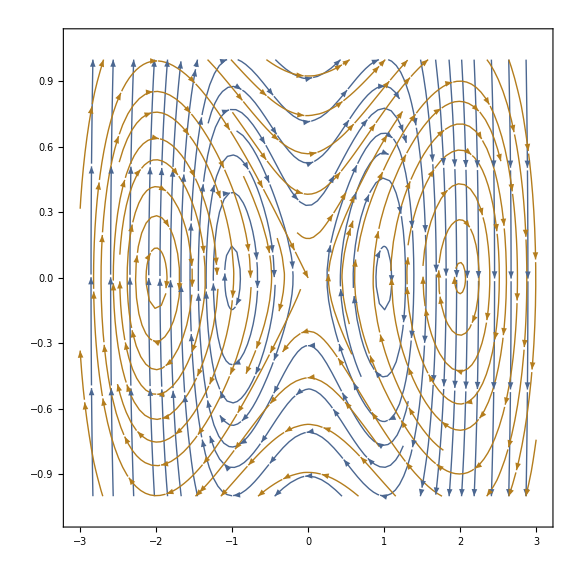

```mathematica
StreamPlot[{{y,(x/1)-(x/1)^3},{y,(x/2)-(x/2)^3}},{x,-3,3},{y,-1,1},ImageSize->Large,Axes->True]
```